```mathematica
SetAttributes[tex,HoldFirst]
tex[exp_]:=TeXForm[HoldForm[exp]]
tf:=TableForm
mf:=MatrixForm
```

# Complex Analysis

Complex Numbers

## Algebra

A complex number is a hybrid object with the properties of both a (two dimensional) vector and a number.

Properties of a vector space

Properties of a number field

Complex Plane

Addition

Multiplication

## Conjugate

## Polar Representation

### Conversion Cartesian ⟷ Polar

```mathematica
CoordinateTransformData["Cartesian"-> "Polar","Mapping", {x,y}]
```

{√(x^2+y^2),ArcTan[x,y]}

```mathematica
CoordinateTransformData["Polar"->"Cartesian","Mapping", {r,φ}]
```

{r Cos[φ],r Sin[φ]}

## Euler’s Formula

## De Moivre’s Theorem

## n-th Roots of Unity

## Complex Exponent

## Complex Logarithm

Differentiation

## Limits

## Continuity

## Derivatives

## Rules for Differentiation

## Cauchy-Riemann Equations

## Analytic Functions

## Harmonic Functions

Elementary Complex Functions

## Polynomials

## Exponential

## Trigonometric

## Hyperbolic

## Logarithmic

Integration

## Contours in the Complex Plane

## Complex Line Integrals

## Cauchy Integral Theorem

## Cauchy Integral Formulas

Series and Residues

## Sequences and Series

### Convergent Series

### Basic Series

### Convergence Theorems

### Absolute Convergence

## Power Series

## Taylor Series

### Example

```mathematica
Series[5/(3+7z),{z,0,5}]//Normal
```

5/3-(35 z)/9+(245 z^2)/27-(1715 z^3)/81+(12005 z^4)/243-(84035 z^5)/729

```mathematica
Series[5/7 1/(3/7+z),{z,0,5}]
```

5/3-(35 z)/9+(245 z^2)/27-(1715 z^3)/81+(12005 z^4)/243-(84035 z^5)/729+O[z]^6

```mathematica
Table[5/7(-1)^k z^k/(3/7)^(k+1),{k,0,5}]
```

{5/3,-(35 z)/9,(245 z^2)/27,-(1715 z^3)/81,(12005 z^4)/243,-(84035 z^5)/729}

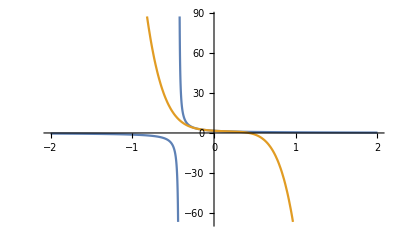

```mathematica
Plot[{5/7 1/(3/7+z),5/3-(35 z)/9+(245 z^2)/27-(1715 z^3)/81+(12005 z^4)/243-(84035 z^5)/729},{z,-2,2}]
```

```mathematica
ComplexPlot3D[5/3-(35 z)/9+(245 z^2)/27-(1715 z^3)/81+(12005 z^4)/243-(84035 z^5)/729,{z,-2-2I,2+2I}]
```

-Graphics3D-

```mathematica
ComplexPlot3D[5/7 1/(3/7+z),{z,-2-2I,2+2I}]
```

-Graphics3D-

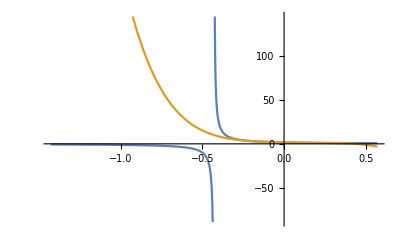

```mathematica
Plot[{5/7 1/(3/7+z),5/3-(35 z)/9+(245 z^2)/27-(1715 z^3)/81+(12005 z^4)/243-(84035 z^5)/729},{z,-10/7,4/7}]
```

```mathematica
?SumConvergence
```

### Cauchy-Hadamard Formula

Add text here ... HOW-TO typeset?

#### Strategy

```mathematica
SeriesCoefficient[-Log[1-z^2],{z,0,n}]
```

Piecewise[{{(1+(-1)^n)/n, n>0}, {0, True}}]

```mathematica
GeneratingFunction[(1+(-1)^(n+1))/(n+1),n,z]
```

-Log[1-z]/z-Log[1+z]/z

```mathematica
MaxLimit[1/Abs[(1+(-1)^(n+1))/(n+1)]^(1/n),n->Infinity]
```

1

```mathematica
ComplexPlot3D[-Log[1-z]/z-Log[1+z]/z,{z,-5-2π ⅈ,5+2π ⅈ}]
```

-Graphics3D-

## Laurent Series

## Zeros and Singularities

## Residues

## Residue Theorem

Temp

## Tmp-1

```mathematica
f[y_,n_]:=D[Cosh[x],{x,n}]/.x:>y
```

```mathematica
f[a,1]
```

Sinh[a]

## Tmp-2

```mathematica
ClearAll[m1,m2,m3];
m1:=({{1, 0, -3}, {0, 1, -1}, {0, 0, 1}});
m2[ϕ_]:=({{Cos[ϕ], Sin[ϕ], 0}, {Sin[ϕ], Cos[ϕ], 0}, {0, 0, 1}});
m3:=({{1, 0, 3}, {0, 1, 1}, {0, 0, 1}});
```

```mathematica
m3.m2[π].m1.{5,1,1}
```

{1,1,1}

```mathematica
ClearAll[m1,m2,m3];
m1:=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
m2[ϕ_]:=({{Cos[ϕ], Sin[ϕ], 0}, {Sin[ϕ], Cos[ϕ], 0}, {0, 0, 1}});
m3:=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
m3.m2[π/2].m1.{2,0,1}
```

{0,2,1}

```mathematica
m3.m2[π/2].m1//mf
```

(0 | 1 | 0
1 | 0 | 0
0 | 0 | 1)

```mathematica
({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).{{2},{0},{1}}//mf
```

(0
2
1)

```mathematica
ClearAll[z,m,α];
z=5+3ⅈ;
m=4+2ⅈ;
m=0;
α=(1+ⅈ)/(√2);
α=(0+ⅈ)/1;
```

```mathematica
ReIm[(z-m)α+m]
```

{-3,5}

## Tmp-3

```mathematica
ClearAll[rc];
rc[f_,{x_,x0_}]:=Reduce[SumConvergence[FullSimplify[SeriesCoefficient[f,{x,x0,n}],n∈Integers&&n≥0] (x-x0)^n,n],Abs[x-x0]]
```

```mathematica
rc[5/(3+7z),{z,0}]
```

Abs[z]<3/7

```mathematica
Reduce[Abs[z]<3/7,z,Complexes]
```

-3/7<Re[z]<3/7&&-1/7 √(9-49 Re[z]^2)<Im[z]<1/7 √(9-49 Re[z]^2)

```mathematica
Reduce[Abs[z]<1,z,Complexes]
```

-1<Re[z]<1&&-√(1-Re[z]^2)<Im[z]<√(1-Re[z]^2)

```mathematica
Reduce[Abs[z-1]<1,z,Complexes]
```

0<Re[z]<2&&-√(2 Re[z]-Re[z]^2)<Im[z]<√(2 Re[z]-Re[z]^2)